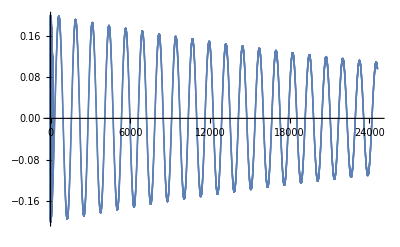

```mathematica
{m,k,d,y0,TMax}={1,1,0.01,0.2,123};
ySol=NDSolveValue[{
m y''[t]==-k y[t] - d y'[t],y[0]==y0,y'[0]==0.0},
y,{t, 0, TMax}];
Data=Table[ySol''[t],{t, 0, TMax, 0.005}];
Show[
ListPlot[Data],
Plot[ySol[t],{t, 0, TMax}]
]
```

```mathematica
1/200.
```

0.005

```mathematica
00
```